# 2D First-Passage time

## Drift towards the equilibrium at (x, xh) = (0, 0) with an absorbing boundary at xh=1. Initial condition is a wide distribution which narrows on approach to the fixed point.

## Write down the nondimensionalized Fokker-Planck equation

```mathematica
FP=λ*D[xh*P[x, xh], x]+D[xh*P[x, xh], xh]-κ*D[x*P[x, xh],xh]+λ*D[P[ x, xh],{x,2}]+D[P[x, xh],{xh,2}]
```

P[x,xh]+xh P^(0,1)[x,xh]-x κ P^(0,1)[x,xh]+P^(0,2)[x,xh]+xh λ P^(1,0)[x,xh]+λ P^(2,0)[x,xh]

## Choose the parameter values

```mathematica
λs = {0.02, 0.045, 0.1, 0.2};
κs = { 0.5,1, 1.9, 4.9};
params = Flatten[Table[{λ->l, κ->k}, {l, λs}, {k, κs}], 1]
legend =  Flatten[Table["λ="<>ToString[l]<>"; "<> "κ="<>ToString[k], {l, λs},{k, κs}], 1];
cstar = Flatten[Table[Re[2*κ/(1+Sqrt[1-4*κ*λ])]/.p, {p, params}]]
products = Table[i*j, {i, λs}, {j, κs}]
```

{{λ→0.02,κ→0.5},{λ→0.02,κ→1},{λ→0.02,κ→1.9},{λ→0.02,κ→4.9},{λ→0.045,κ→0.5},{λ→0.045,κ→1},{λ→0.045,κ→1.9},{λ→0.045,κ→4.9},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.1,κ→1.9},{λ→0.1,κ→4.9},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.2,κ→1.9},{λ→0.2,κ→4.9}}

{0.505103,1.02084,1.97827,5.50641,0.511787,1.04957,2.09809,7.29432,0.527864,1.12702,2.55051,5.,0.563508,1.38197,2.5,2.5}

{{0.01,0.02,0.038,0.098},{0.0225,0.045,0.0855,0.2205},{0.05,0.1,0.19,0.49},{0.1,0.2,0.38,0.98}}

## Set up the mesh, boundary conditions, and initial condition

#### Choose the same initial width for every parameter set: the one with the largest s.s. width in x

```mathematica
Table[1/(2κ)+((1+κ) λ)/(2κ)/.p, {p, params}]
```

{1.03,0.52,0.278421,0.114082,1.0675,0.545,0.2975,0.129133,1.15,0.6,0.339474,0.162245,1.3,0.7,0.415789,0.222449}

```mathematica
varCheck =  {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[13]]
```

{{1.3,1/2},{1/2,0.75}}

```mathematica
varChoice=13;
```

```mathematica
xStds = Table[Sqrt[ 1/(2κ)+((1+κ) λ)/(2κ)]/.params[[varChoice]],Length[params]]
xhStds = N[Table[ Sqrt[(1+κ)/2]/.p, {p, params}]]
```

{1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018,1.14018}

{0.866025,1.,1.20416,1.71756,0.866025,1.,1.20416,1.71756,0.866025,1.,1.20416,1.71756,0.866025,1.,1.20416,1.71756}

#### Boundary condition at x*=1, y* = 2k/(1+Sqrt(1-4*l*k))

```mathematica
Needs["NDSolve`FEM`"]
```

```mathematica
x0 = 8;
xh0=8;
xls=-5*xStds
xrs = x0+5*xStds
xhls=cstar
xhrs = x0+5*xhStds
```

{-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088,-5.70088}

{13.7009,13.7009,13.7009,13.7009,13.7009,13.7009,13.7009,13.7009,13.7009,13.7009,13.7009,13.7009,13.7009,13.7009,13.7009,13.7009}

{0.505103,1.02084,1.97827,5.50641,0.511787,1.04957,2.09809,7.29432,0.527864,1.12702,2.55051,5.,0.563508,1.38197,2.5,2.5}

{12.3301,13.,14.0208,16.5878,12.3301,13.,14.0208,16.5878,12.3301,13.,14.0208,16.5878,12.3301,13.,14.0208,16.5878}

```mathematica
icPos = Table[{x0,xh0}, {c, cstar}];
icVar = {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[varChoice]] ;
ic0 = N[Table[PDF[MultinormalDistribution[pos,icVar], {x, xh}], {pos, icPos}]];(*ic0 : Choose widest s.s. distribution of the parameter values*)
(*icSS = N[Table[PDF[MultinormalDistribution[icPos,{{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.p], {x, xh}], {p, params}]];*)
(*icSS : Choose s.s. distribution width for each of the parameter values*)
bcFunc[xl_, xr_, xhl_, xhr_] :={P[xl, xh]==0,
           P[xr, xh]==0,
           P[x, xhr]==0,
           P[x, xhl]==0
}
ΩFunc[xl_, xr_, xhl_, xhr_] :=ImplicitRegion[True,{{x,xl,xr},{xh,xhl,xhr}}];
bcs = MapThread[bcFunc, {xls, xrs, xhrs, xhls}];
minFunc[xStd_, xhStd_]:=Min[6*xStd, 6*xhStd]/300;
cellDistances = MapThread[minFunc, {xStds, xhStds}]
Ω=MapThread[ΩFunc,{xls, xrs, xhls, xhrs}];
```

{0.0173205,0.02,0.0228035,0.0228035,0.0173205,0.02,0.0228035,0.0228035,0.0173205,0.02,0.0228035,0.0228035,0.0173205,0.02,0.0228035,0.0228035}

```mathematica
xhCheckFunc[xhl_, c_]:=c≤ xhl
```

```mathematica
MapThread[xhCheckFunc, {x0-4*xhStds, cstar}]
```

{True,True,True,False,True,True,True,False,True,True,True,False,True,True,True,False}

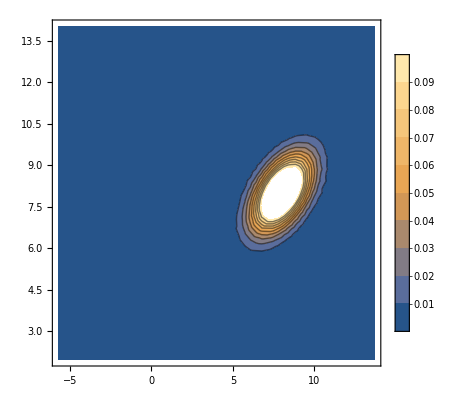

```mathematica
toPlot=3;
ContourPlot[ic0[[toPlot]], {x, xls[[toPlot]], xrs[[toPlot]]}, {xh, xhls[[toPlot]], xhrs[[toPlot]]}, PlotRange->{0, 0.1}, PlotLegends->Automatic]
```

General::munfl: 1/2.71828^2477.11 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^2103.98 is too small to represent as a normalized machine number; precision may be lost.

General::munfl: 1/2.71828^1492.22 is too small to represent as a normalized machine number; precision may be lost.

General::stop: Further output of General::munfl will be suppressed during this calculation.

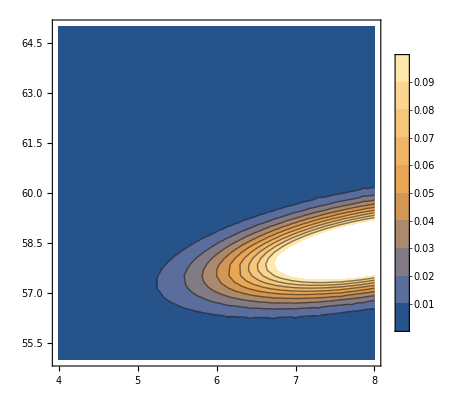

```mathematica
toPlot=8;
ContourPlot[ic0[[toPlot]], {x, 4, 8}, {xh, 55, 65}, PlotRange->{0, 0.1}, PlotLegends->Automatic]
```

## Calculate the time-integrated probability distribution and the flux through the boundary

```mathematica
NDSolverParams[param_, ic_, bc_, reg_, cell_] :=Module[{N},
N = NDSolve[Join[{(FP/. param)==-ic}, bc],
                                   P,{x, xh}∈reg, 
Method->{"FiniteElement", "MeshOptions"->{"MaxCellMeasure"->cell}}];
Return[(P/.N[[1]])];
]
```

```mathematica
(*solsSS=MapThread[NDSolverParams, {params, icSS, bcs, meshes}];*)
solsIc0=MapThread[NDSolverParams, {params, ic0, bcs, Ω, cellDistances}];
```

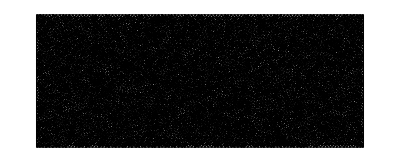

```mathematica
solsIc0[[1]]["ElementMesh"]["Wireframe"]
```

```mathematica
(*fluxSS = Table[Derivative[0,1][sol],{sol, solsSS}];*)
fluxXIc0 = Table[Derivative[0,1][sol],{sol, solsIc0}];
```

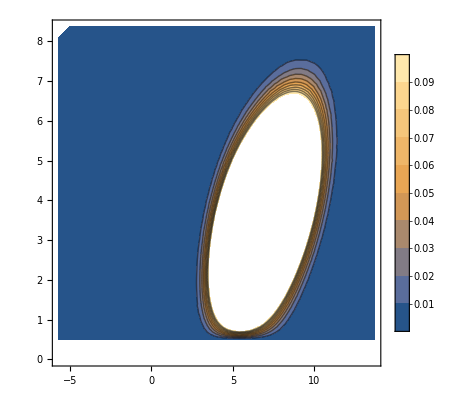

```mathematica
toShow = 1;cIc0 =ContourPlot[solsIc0[[toShow]][x, xh], {x, xls[[toShow]], xrs[[toShow]]}, {xh, xhls[[toShow]], xhrs[[toShow]]}, PlotLegends->Automatic, PlotRange->{0, 0.1}];
(*Show[cSS]*)
Show[cIc0]
```

```mathematica
XIc0 =MapThread[#1[x,#2]&,{fluxXIc0,cstar}];
```

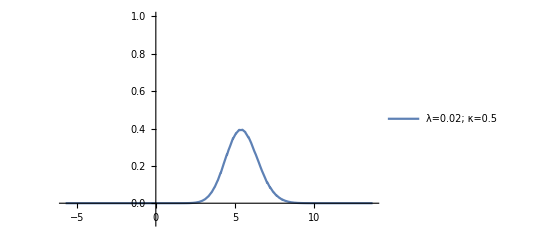

```mathematica
Plot[XIc0[[1]], {x, -20, 20}, PlotRange->{-0.1, 1}, PlotLegends->legend]
```

```mathematica
(*normsSS = Table[NIntegrate[xp, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
meansSS= Table[NIntegrate[xp*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}]
secondSS = Table[NIntegrate[xp*x*x, {x, -10, 15}, WorkingPrecision->10], {xp, XSS}];
varsSS= secondSS-meansSS^2
diffSS = varsSS/meansSS;*)
```

```mathematica
NIntegrate[XIc0[[1]], {x, 1, 10}, WorkingPrecision->8]
```

0.98968067

```mathematica
IntegFunc[f_, l_, r_] := NIntegrate[f, {x, l, r}, WorkingPrecision->10]
```

```mathematica
normsIc0 = MapThread[IntegFunc, {XIc0, xls, xrs}]
meansIc0= MapThread[IntegFunc, {XIc0*x, xls, xrs}]
secondIc0 = MapThread[IntegFunc, {XIc0*x*x, xls, xrs}]
varsIc0 = secondIc0-meansIc0^2
diffIc0 = varsIc0/meansIc0;
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.809781171}. NIntegrate obtained 0.9927624985 and 0.0004673502004 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.536138094}. NIntegrate obtained 0.998005212 and 0.0007512992513 for the integral and error estimates.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {1.081409479}. NIntegrate obtained 1.000165163 and 0.001733804877 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{0.9899459798,0.9927624985,0.998005212,1.000165163,0.9953107761,0.9987878041,1.001168674,-6.083124778×10^30,0.9986169647,1.00211486,1.000985824,0.9404274987,1.000664456,1.001557428,0.9909157033,0.745086897}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.06866958}. NIntegrate obtained 5.400781803 and 0.001409802733 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {3.809781171}. NIntegrate obtained 2.821879456 and 0.001387508602 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.445595325}. NIntegrate obtained 1.686640173 and 0.0009193334528 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{5.400781803,2.821879456,1.686640173,1.051226456,4.751283608,2.400569093,1.40886041,-5.935847926×10^30,3.949794368,1.880714872,1.076794257,-0.3001097104,3.084567151,1.29777364,0.08777147337,-1.062524496}

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {7.06866958}. NIntegrate obtained 30.48750752 and 0.01006423968 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {4.226615735}. NIntegrate obtained 8.439389838 and 0.004768959662 for the integral and error estimates.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

NIntegrate::ncvb: NIntegrate failed to converge to prescribed accuracy after 9 recursive bisections in x near {x} = {2.445595325}. NIntegrate obtained 3.024039855 and 0.002857859538 for the integral and error estimates.

General::stop: Further output of NIntegrate::ncvb will be suppressed during this calculation.

{30.48750752,8.439389838,3.024039855,1.164810125,24.01326483,6.32161646,2.228398642,-6.350577409×10^30,17.4136546,4.266459474,1.494963452,0.2776249685,11.82257104,2.619366148,0.5008237708,1.771191908}

{1.3190634,0.47638618,0.17928478,0.059733064,1.4385689,0.55888449,0.24351099,-3.52342906×10^61,1.812779,0.72937105,0.33547758,0.18755913,2.3080165,0.935149728,0.493119939,0.642233604}

```mathematica
normsIc0[[8]]=1;
varsIc0[[8]]=1;
meansIc0[[8]]=1;
```

```mathematica
grid = Flatten[Table[{l, s}, {l, λs}, {s, κs}], 1];
params
```

{{λ→0.02,κ→0.5},{λ→0.02,κ→1},{λ→0.02,κ→1.9},{λ→0.02,κ→4.9},{λ→0.045,κ→0.5},{λ→0.045,κ→1},{λ→0.045,κ→1.9},{λ→0.045,κ→4.9},{λ→0.1,κ→0.5},{λ→0.1,κ→1},{λ→0.1,κ→1.9},{λ→0.1,κ→4.9},{λ→0.2,κ→0.5},{λ→0.2,κ→1},{λ→0.2,κ→1.9},{λ→0.2,κ→4.9}}

```mathematica
(*normArraySS = ArrayReshape[normsSS, {5, 5}];
varArraySS = ArrayReshape[varsSS, {5, 5}];
meanArraySS = ArrayReshape[meansSS, {5, 5}];
diffArraySS = ArrayReshape[diffSS, {5, 5}];*)
normArrayIc0 = ArrayReshape[normsIc0, {4,4}];
varArrayIc0 = ArrayReshape[varsIc0, {4,4}];
meanArrayIc0 = ArrayReshape[meansIc0, {4,4}];
diffArrayIc0 = ArrayReshape[diffIc0, {4,4}];
```

```mathematica
cf[x_]:=Blend[{{-2, Red},{ 1,White},{5,Blue}}, x]
```

```mathematica
xticks = Transpose[{{1, 2, 3, 4}, λs}];
yticks = Transpose[{{1, 2, 3, 4}, κs}];
```

```mathematica
ArrayPlot[varArrayIc0, ColorFunction->(Blend[{{-1, Red},{ 0,White},{1,Blue}},#]&), PlotLegends->{Placed[BarLegend[Automatic,None,LegendLabel->"var(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[ArrayReshape[Table[Blend[{{-2, Red},{ 0,White},{5,Blue}}, i],{i,Flatten[meanArrayIc0]}], {4,4}], PlotLegends->{Placed[BarLegend[{cf[#]&,{-2, 5}},LegendLabel->"mean(x)"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]

ArrayPlot[normArrayIc0, ColorFunction->(Blend[{White,Blue},#]&), PlotLegends->{Placed[BarLegend[Automatic,Automatic,LegendLabel->"norm(e(x))"],Right]}, FrameTicks->{xticks, yticks}, DataReversed->True, FrameLabel->{λ, κ}]
```

-Graphics-

-Graphics-

-Graphics-

```mathematica
A3= {{ 0,λ},{-κ, 1}}/. {λ->0.2,κ->4.9}
B3 = {{Sqrt[λ],0},{0,1 }}/.  {λ->0.2,κ->4.9}
s0 = {{1/(2κ)+((1+κ) λ)/(2κ),1/2},{1/2,(1+κ)/2}}/.params[[13]]
```

{{0,0.2},{-4.9,1}}

{{0.447214,0},{0,1}}

{{1.3,1/2},{1/2,0.75}}

```mathematica
S[t_] = FullSimplify[MatrixExp[A3].s0.MatrixExp[Transpose[A3]]+Integrate[MatrixExp[-Integrate[A3, {s, tp, t}]].B3.Transpose[B3].MatrixExp[-Integrate[Transpose[A3], {s, tp, t}]], {tp, 0, t}]]
```

{{(0.553155-7.96076×10^-18 ⅈ)+ⅇ^(-1. t) ((-0.161644+6.09102×10^-18 ⅈ)-(0.0608051-1.86974×10^-18 ⅈ) Cos[1.7088 t]-(0.0131373-4.65868×10^-18 ⅈ) Sin[1.7088 t]),(-3.11232-1.46509×10^-16 ⅈ)+ⅇ^(-1. t) ((-0.40411+1.02883×10^-16 ⅈ)-(0.0958904-4.3626×10^-17 ⅈ) Cos[1.7088 t]-(0.292603-3.3761×10^-17 ⅈ) Sin[1.7088 t])},{(-3.11232-3.91934×10^-18 ⅈ)+ⅇ^(-1. t) ((-0.40411+3.86223×10^-17 ⅈ)-(0.0958904+3.47029×10^-17 ⅈ) Cos[1.7088 t]-(0.292603-3.80276×10^-17 ⅈ) Sin[1.7088 t]),(58.6064-4.54614×10^-16 ⅈ)+ⅇ^(-1. t) ((-3.96027+6.17042×10^-16 ⅈ)+(1.01027-1.62427×10^-16 ⅈ) Cos[1.7088 t]-(1.14115-2.33557×10^-16 ⅈ) Sin[1.7088 t])}}

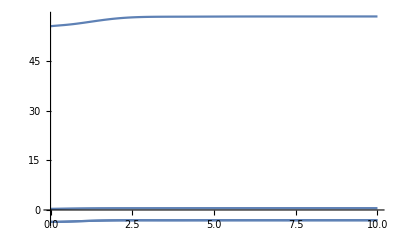

```mathematica
Plot[Re[S[t]], {t, 0, 10}]
```

```mathematica
Re[0.5+0.5*I]
```

0.5